## Section | Dissipative interactions and open quantum systems

The chapter begins by discussing the concept of decoherence and dissipation, emphasizing that while the evolution of isolated quantum systems is unitary and preserves coherence, real-world systems are rarely isolated. We describe the mathematical formalism of open quantum systems, the role of the density matrix in describing mixed states, and the master equation approach to modeling decoherence dynamics. The chapter also explores specific examples, such as the decoherence of superposition states (e.g., Schrödinger cat states) and other phenomena that can be described by master equations.

### Key concepts

Lindblad master equation

Decoherence

Modeling open quantum systems

Workflow for solving master equations

### Quantum jump approach and decoherence

Quantum theory was initially developed as a theory based on ensembles because it was thought that manipulating single quantum systems (like one electron or one atom) was impossible. In 1975 Dehmelt proposed in the context of fluorescence spectroscopy some schemes for measuring transition frequencies that required single quantum system observations, that were later implemented using single ion traps. Predictions were confirmed by experiments that impulsed the development of the quantum jump approach

#### Algorithm for general quantum jump

The quantum jump method is similar to Monte Carlo methods, and we assume a cavity field at T = 0 K and a photon emission means the field loses one photon represented by an annihilation operator

Calculate the current probability ΔP of emission of a photon in a time interval δt according to Δ P=γ ⟨ψ|(â)^†â|ψ⟩ δ t where |ψ⟩ is one member of the ensemble

Obtain a random number 0 ≤ r < 1, compare with ΔP to decide emission

Emit if r < ΔP (field loses one photon), the system jumps to renormalized form |ψ⟩→|ψ_emit⟩=(â|ψ⟩)/(⟨ψ|(â)^†â|ψ⟩^(1/2))

No emission r > ΔP, the system evolves according to
|ψ⟩→|ψ_(no emit)⟩=(e^(-ⅈ δ t H_eff)|ψ⟩)/([⟨ψ|e^(ⅈ δ t H_eff^†) e^(-ⅈ δ t H_eff)|ψ⟩]^(1/2))=(e^(-ⅈ δ t H_eff)|ψ⟩)/([⟨ψ|e^(-γ δ t (â)^†â)|ψ⟩]^(1/2))
≈([1-(ⅈ/ℏ)Ĥ δ t-(γ/2)δ t (â)^†â]|ψ⟩)/(1-Δ P)^(1/2)
where (Ĥ)_eff=Ĥ-ⅈ ℏ (γ/2)(â)^†â is the effective non Hermitian Hamiltonian describing non unitary evolution where the second term represents decay of the cavity field.

Iterate the process to record a trajectory of conditional evolution of one member of the ensemble with jump events  t_(1,)t_2...

Average observables over a big number of trajectories to get average behavior or whole ensemble

#### Quantum jumps on familiar states

Assuming no interaction (Ĥ = 0) so only the dissipation acts. If we have an initial cavity field in a coherent state |α⟩ the jump evolution leaves the field unchanged because a coherent state is eigenstate of the annihilation operator, and the no jump-evolution results:

(e^(-(γ/2)δ t a^†a)|α⟩)/(√⟨α|e^(-γ δ t a^†a)|α⟩)=|α e^(-γ δ t/2)⟩

Set truncation size:

```mathematica
SetFockSpaceSize[20];
```

Term describing non unitary evolution:

```mathematica
Hdisp = - ⅈ h (γ/2) SuperDagger[a]@a;
```

We will verify the no-jump evolution symbolically.  We get a valid relation because the square root in the denominator  just a normalizing factor, quantum state equality in Wolfram QuantumFramework work up to global phases and multiplicative factors.

Symbolic comparison:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ CoherentState[][α]  == CoherentState[][α ⅇ^(-γ δt /2)]
```

True

The coherent state remains a coherent state after the evolution, however, the amplitude of the state has an exponential decay due to the non unitary Hamiltonian

Non-unitary Hamiltonian:

```mathematica
Hdisp["UnitaryQ"]
```

False

If we now consider a cavity field prepared in a even cat state  (|ψ⟩)_e=𝒩_e(|α⟩+|-α⟩) where 𝒩_e   is  a normalization constant , the annihilation operator converts an even cat state to odd cat state

Photon distribution corresponds to odd cat state after jump:

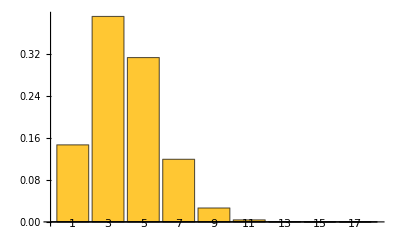

```mathematica
(a @ CatState[][2.,0])["ProbabilityPlot"]
```

For a no jump transition the field state decays referred as “jumping-cat” transition

exp(-γ δ t (â)^†â/2)(|α⟩±|-α⟩)=(|α e^(-γ δ t/2)⟩±|-α e^(-γ δ t/2)⟩)

We will also verify this symbolically without normalizing, that is why we will not use CatState (which comes normalized). Instead we just define a superposition of non normalized coherent states

Coherent state superposition:

```mathematica
evenCat = QuantumState[CoherentState[][α]+CoherentState[][-α],"Parameters"->α];
```

“No-jump” evolution:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ evenCat  == evenCat[α ⅇ^(-γ δt /2)]
```

True

The cat state “reduce”  during no-jump evolution (the amplitude decays)

### Decoherence

It can be defined as the transformation over time of a quantum mechanical superposition into a classical statistical mixture, as a result of interaction with an environment. As an example, consider  an initial even cat state , the cavity-environment state is

|ψ(0)⟩∝(|α⟩+|-α⟩)|ϵ⟩

where |ϵ ⟩ is the quantum state of the environment. The environment can be described  with an arbitrary number of systems and states which are not relevant for the analysis. At a later time the system will evolve to

|ψ(t)⟩∝(|β⟩(|ϵ⟩)_1+|-β⟩(|ϵ⟩)_2)

such that β=α e^(-γ t/2)   from the previous section, so that the field becomes entangled with the environment. If we compute the density operator and trace over a complete set of states of the environment ⟨ϵ_i|ϵ_j⟩=δ_ij, we get a reduced field density operator

ρ_F(t)=Tr_Env ρ(t)=∑_i ⟨ϵ_i|ρ|ϵ_i⟩=|β(t)⟩⟨β(t)|+|-β(t)⟩⟨-β(t)|

is a statistical mixture of two coherent states

#### Quantum jump implementation

Setup simulation parameters:

```mathematica
dim=8;
γ=0.5;
δt=0.01;
steps=600;
```

Annihilation and number operators:

```mathematica
a=Table[If[j==i+1,Sqrt[i],0],{i,dim},{j,dim}];
nOp=ConjugateTranspose[a].a;
```

Non-Hermitian Hamiltonian and deterministic evolution, we assume pure dissipation so the coherent Hamiltonian is zero:

```mathematica
Heff=-I*(γ/2)*nOp;
U0=MatrixExp[-I*Heff*δt];
```

Consider as an initial state |4⟩:

```mathematica
ψInitial=UnitVector[dim,5];
```

Implement the jump function, based on the algorithm that was described before:

```mathematica
takeStep[ψ_]:=Module[{ΔP,ψNew},ΔP=γ*δt*Re[Conjugate[ψ].nOp.ψ];
If[RandomReal[]<ΔP,(*JUMP*)ψNew=a.ψ,(*NO JUMP*)ψNew=U0.ψ];
ψNew/Norm[ψNew]]
```

Run the quantum jump algorithm for 600 trajectories, and track the mean photon number for each trajectory and calculate the average of all trajectories:

```mathematica
numTrajectories=600;
Print["Simulating ",numTrajectories," trajectories..."];
allTrajectories=Table[NestList[takeStep,ψInitial,steps],{numTrajectories}];
Print["Simulation completed. "]
allPhotonNumbers=Map[Function[traj,Map[Re[Conjugate[#].nOp.#]&,traj]],allTrajectories];
averagePhotonNumbers=Mean[allPhotonNumbers];
```

Simulating 600 trajectories...

Simulation completed.

Plot the results:

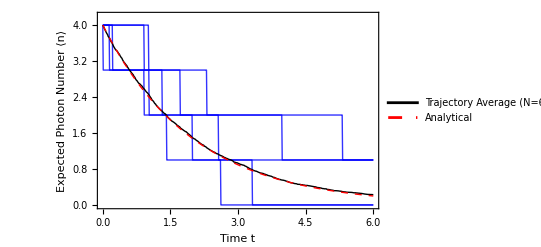

```mathematica
Show[ListLinePlot[Take[allPhotonNumbers,5],],ListLinePlot[averagePhotonNumbers,DataRange->{0,steps δt},],Plot[4 Exp[-γ t],{t,0,steps δt},],]
```

Observing a single quantum trajectory reveals a sequence of discrete, random downward steps, directly mirroring the isolated ‘clicks’ of a photon detector. However, when we average these individual trajectories over a large ensemble, the discrete jumps wash out, giving rise to smooth, continuous evolution. This emergent average behavior perfectly recovers the expected exponential decay, ⟨(n⟩)_(t=0)ⅇ^(-γ t). It is precisely this ensemble-averaged dynamic that is captured by a master equation, which we will formalize next

### Master equation for density operators

The history of a particular trajectory splits into two alternatives in a time Δt to allow at most one jump, either it jumps or it does not

|ψ⟩→Piecewise[{{(|ψ⟩)_emit, with probability   Δ P}, {(|ψ⟩)_(no emit), with probability   1-Δ P}}]

For a pure state |ψ⟩⟨ψ| the evolution can be described as a sum of two outcomes:

|ψ⟩⟨ψ|→Δ P |ψ_emit⟩⟨ψ_emit|+(1-Δ P)|ψ_(no emit)⟩⟨ψ_(no emit)|

=γ δ t â|ψ⟩⟨ψ|(â)^†+[1-ⅈ/ℏ Ĥ δ t-γ/2 δ t (â)^†â]|ψ⟩⟨ψ|[1+ⅈ/ℏ Ĥ δ t-γ/2 δ t (â)^†â]

≈|ψ⟩⟨ψ| -ⅈ/ℏδ t [Ĥ,|ψ⟩⟨ψ|]
+γ/2δ t (2 â|ψ⟩⟨ψ|(â)^†-(â)^†â|ψ⟩⟨ψ|-|ψ⟩⟨ψ|(â)^†â)

Averaging  over all the members of the ensemble:

ρ̂(t+δ t)=ρ̂(t)-ⅈ/ℏδ t [Ĥ,ρ̂]+γ/2 δ t (2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

Taking the limit as δt → 0 we get a differential equation

(d ρ̂)/dt=-ⅈ/ℏ[Ĥ,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

Referred as the master equation which can also be obtained from more complicated methods for the T=0K damping problem

This is a particular case of a more general equation called the Lindblad equation

ρ̇=-ⅈ [H,ρ]+ ∑_n γ_n(L_n ρ L_n^†-1/2{L_n^†L_n,ρ})

where L_n are called jump operators representing the effects of the environment, and those operators have particular γ_n rates

Considering just  n=1 with the jump operator â (related to photon loss) with rate γ we get the previous equation:

```mathematica
-ⅈ/h HoldForm[Commutator[H,ρ]]+Simplify[γ(a**ρ**SuperDagger[a]-1/2 Anticommutator[SuperDagger[a]**a,ρ])]
```

-(ⅈ Commutator[H,ρ])/h+1/2 γ (2 a**ρ**a^†-ρ**a^†**a-a^†**a**ρ)

The whole equation can be cast in super-operator form, such that the right hand side is the Lindblad super-operator ℒ applied to some density operator ρ

ρ̇=ℒ[ρ]

The Lindblad master equation is a matrix differential equation. Most standard numerical ODE solvers (like Runge-Kutta) are designed to solve systems of vector differential equations. Therefore, we need a mathematical trick to reshape our N × N  density matrix ρ into an N^2×  1 column vector denoted as |ρ⟩⟩. Consequently, the operators acting on ρ from the left and right must be upgraded into an N^2× N^2 super-operator matrix.

One convention is to use row-stacking (stack rows of a matrix into a vector)

ρ=(ρ_11 | ρ_12
ρ_21 | ρ_22)   →^vec_R    |ρ⟩⟩=(ρ_11
ρ_12
ρ_21
ρ_22)

Using row-stacking vectorization we can express the terms of the Lindblad equation that will act on the vectorized density operator as

-ⅈ[H,ρ]->-ⅈ(H⊗𝕀-𝕀⊗H^T)
𝒟_vec[L_μ]=L_μ⊗L_μ^*-1/2(L_μ^†L_μ⊗𝕀+𝕀⊗(L_μ^†L_μ)^T)

Dissipator contribution, represent each of the terms in the sum of Lindblad equation, this definition includes the case L_i≠ L_j (non-diagonal form of Lindblad equation) but we will stick to the case 𝒟(L_i)

```mathematica
ClearAll[𝒟]
𝒟[Lj_,Lk_]:=KroneckerProduct[Lj,Conjugate[Lk]]-1/2(KroneckerProduct[ConjugateTranspose[Lk].Lj,IdentityMatrix[Length[Lk]]]+KroneckerProduct[IdentityMatrix[Length[Lk]],Transpose[ConjugateTranspose[Lk].Lj]])
𝒟[Lj_]:=𝒟[Lj,Lj]
```

Lindbladian builder:

```mathematica
Lindbladian[h_,lk_,γk_?VectorQ]:=-ⅈ(KroneckerProduct[h,IdentityMatrix[Length@h]]-KroneckerProduct[IdentityMatrix[Length@h],Transpose@h])+γk.Map[𝒟,lk]
```

We can use “Liouvillian” in QuantumOperator to get those super-operators, for example consider a two level system with H=σ_z , L_1=σ_x with rate γ:

```mathematica
ℒ =QuantumOperator["Liouvillian"[QuantumOperator["Z"],{QuantumOperator["X"]},{γ}]]
```

-γ0000+(-2 ⅈ-γ)0011+γ0101+γ0110+γ1001+γ1010+(2 ⅈ-γ)1100-γ1111

ℒ is a super-operator:

```mathematica
ℒ["Type"]
```

Superoperator

Check the dimensions of the super-operator matrix:

```mathematica
ℒ["Matrix"]//Dimensions
```

{4,4}

Get the matrix of the Lindbladian using the manual builder:

```mathematica
Lindbladian[PauliMatrix[3],{PauliMatrix[1]},{γ}]//MatrixForm
```

(-γ | 0 | 0 | γ
0 | -2 ⅈ-γ | γ | 0
0 | γ | 2 ⅈ-γ | 0
γ | 0 | 0 | -γ)

Verify we get the same result compared to the matrix of the Super-operator object:

```mathematica
ℒ["Matrix"]-Lindbladian[PauliMatrix[3],{PauliMatrix[1]},{γ}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Dissipative interactions from master equations

#### Dissipation of a coherent state

Set the cutoff size:

```mathematica
SetFockSpaceSize[15];
```

Initial parameters for a coherent state |α⟩ with |α| equal to 2:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0=CoherentState[][αcoh];
```

Establishing a damping parameter:

```mathematica
γ = RandomReal[{1,2}];
```

Setting up the Liouvillian master equation with Ĥ= (â)^†â and L_1=â:

```mathematica
ℒ= QuantumOperator["Liouvillian"[SuperDagger[a]@a,{a},{γ}]];
```

Computing the evolution numerically (ⅈ included for super-operators):

```mathematica
ρt=QuantumEvolve[ⅈ ℒ,ρ0,{t,0,1}];
```

Extra variables for computing the evolution statistics:

```mathematica
time=Range[0,1,0.01];
fock=Range[$FockSize]-1;
```

Computing mean number of photons and the fidelity with respect to an analytical solution (that remains a coherent state):

```mathematica
qs=QuantumSimilarity[CoherentState[][αcoh ⅇ^(-ⅈ #) ⅇ^(-1/2 # γ)],ρt[#]]&/@time;
meanN=Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]&/@time;
```

Plotting the statistics, the evolved state behaves like the analytical solution with an exponential decay in the mean number of photons:

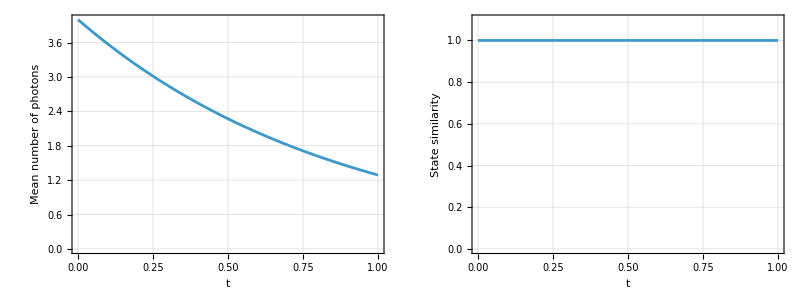
-Graphics-Evolution statistics of a coherent state

```mathematica
Labeled[Grid[{{ListLinePlot[Thread[{time,meanN}],],ListLinePlot[Thread[{time,qs}],]}}],]
```

|α|^2 ⅇ^(-γ t) is the functional form of the mean photon number curve. Then the decay time of the field energy is T_decay=1/γ

Do an exponential decaying fit:

```mathematica
nlm =NonlinearModelFit[Thread[{time,meanN}],k Exp[-g t],{k,g},{t}];
```

Fitted equation:

```mathematica
nlm["Function"][t]
```

3.99977 ⅇ^(-1.13275 t)

Compare the parameters:

```mathematica
(g /. nlm["BestFitParameters"]) - γ
```

4.22831×10^-9

Spiral motion of the center of the Wigner representation of the coherent state, the Hamiltonian with unit frequency makes the coherent state rotate, and the dissipation  makes it go towards the origin:

-Graphics-

#### Decoherence of an even cat : becoming statistical mixture

```mathematica
SetFockSpaceSize[15];
```

Now we analyze the evolution of  a cavity prepared with an even cat state:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0 = CatState[][αcoh,0];
```

Setting a pure decoherence master equation with photon loss (H = 0):

```mathematica
γ = 0.9;
ℒ= QuantumOperator["Liouvillian"[None,{a},{γ}]];
```

Evolving the state:

```mathematica
ρt = QuantumEvolve[ⅈ ℒ, ρ0, {t,0,10}];
```

Monitoring how the traces change. Tr[(ρ̂)^2]is related to the purity and also a measure of decoherence. But there will be a point that purity starts to increase, because the decay in energy makes state become the vacuum (pure state) :

Sampling time:

```mathematica
time=Range[0,10,0.01];
```

Compute trace and purity:

```mathematica
traces = Table[{Tr[ρt[t]],ρt[t]["Purity"]},{t,time}];
```

Plot result:

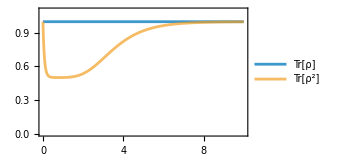

```mathematica
ListLinePlot[Thread[{time,#}]&/@Transpose[traces]
,]
```

The energy decay (mean photon number) still decays exponentially as expected :

```mathematica
meanPhotons = Table[{t,Dot[fock,Diagonal[ρt[t]["DensityMatrix"]]]},{t,time}] ;
```

Plot the curve:

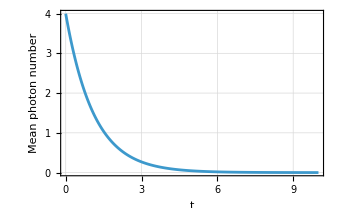

```mathematica
ListLinePlot[meanPhotons,]
```

The theoretical solution of the master equation  is:

ρ_F(t)=𝒩_e^2 [|α e^(-γ t/2)⟩⟨α e^(-γ t/2)|+|-α e^(-γ t/2)⟩⟨-α e^(-γ t/2)|
+e^(-2(|α|)^2(1-e^(-γ t)))(|α e^(-γ t/2)⟩⟨-α e^(-γ t/2)|+|-α e^(-γ t/2)⟩⟨α e^(-γ t/2)|)]

Implement analytical solution:

```mathematica
sol =With[{α=αcoh ⅇ^(1/2 (-γ) t),decay=ⅇ^(-2 Abs[αcoh]^2 (1-ⅇ^(-γ t)))},With[{cPlus=CoherentState[][α],cMinus=CoherentState[][-α]},QuantumState[(cPlus["MatrixState"]+cMinus["MatrixState"]+QuantumOperator[(decay (cPlus@SuperDagger[cMinus]+cMinus@SuperDagger[cPlus]))]["MatrixQuantumState"]),"Parameters"->t]["Normalize"]]];
```

Compute fidelity as function of time:

```mathematica
AbsoluteTiming[similarities = Table[QuantumSimilarity[ρt[t],sol[t]],{t,0,10,0.05}];]
```

{27.66,Null}

Verifying are the same(basically 1 with  numerical error):

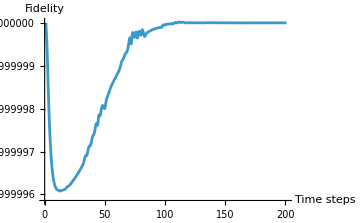

```mathematica
ListLinePlot[similarities,]
```

Apart  from the energy decay we can see there is another quantity that decays,  the the value of e^(-2(|α|)^2(1-e^(-γ t))) multiply the “coherences”(off diagonal elements). For short times a decoherence time is obtained from an expansion T_decoh=1/(2 γ (|α|)^2)=T_decay/(2(|α|)^2). Such that T_decoh<T_decay as long as |α|^2>0.

This can be visualized with the Wigner representation, using some time in between T_decay and T_decoh:

```mathematica
Tevol = 1/(2γ);
```

Statistical mixture of coherent states:

```mathematica
ρmix = Mean[CoherentState[][#]["MatrixState"]&/@{αcoh,-αcoh}];
```

Plot the Wigner function:

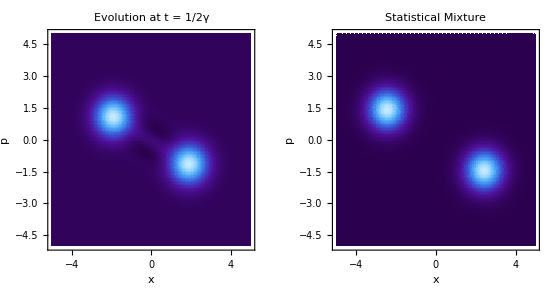

```mathematica
GraphicsRow[Table[wig = WignerRepresentation[s[[1]],{-5,5},{-5,5}];DensityPlot[wig[x,p],{x,-5,5},{p,-5,5},],{s,{{ρt[Tevol],"Evolution at t = 1/2γ"},{ρmix,"Statistical Mixture"}}}],]
```

This verifies that the “coherences” decay faster than the energy and the evolved state becomes a statistical mixture, of course the amplitude is not the same because during the evolution  photon loss has acted

But after a sufficient time the photon loss transforms the state into the vacuum:

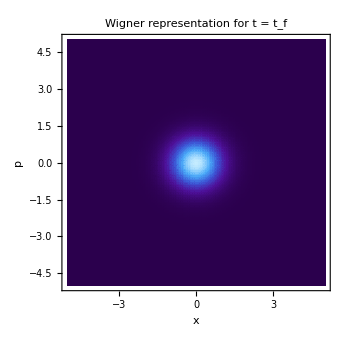

```mathematica
wig = WignerRepresentation[ρt[10],{-5,5},{-5,5}]; DensityPlot[Chop@wig[x,p],{x,-5,5},{p,-5,5},]
```

### Generation of coherent states from decoherence: optical balance

Dissipation destroys coherence in quantum superposition effects. However, even if it does not sound intuitive, it is also possible to create coherence from dissipative effects. The master equation has unitary(the commutator)and non-unitary terms(dissipation) with nonlinear behavior in the creation and annihilation operators. The interactions can “balance each other” such that the evolution at t → ∞  is  a different state than the vacuum.

Considering an interaction Hamiltonian OverHat[H_I] = h G(â+(â)^†)  where G is the strength of a classical pump field that propagates in a photon absorbing medium (dissipation). The master equation using photon loss channel becomes:

(d ρ̂)/dt=-ⅈG[â+(â)^†,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

We start with a random cavity field:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize];
```

Establishing simulation parameters, driving strength and photon loss rate:

```mathematica
G = RandomReal[{1,2}];
γ  = RandomReal[{1.5,2}];
```

For the Liouvillian of the master equation we now consider a driving interaction term so Ĥ≠ 0:

```mathematica
ℒ= QuantumOperator["Liouvillian"[G(a+SuperDagger[a]),{a},{γ}]];
```

Solving the master equation numerically:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,ρ0,{t,0,3}];
```

The steady-state solution of the equation converges to ρ = | β ⟩ ⟨β | where 
β = - 2 ⅈ G/γ

Compute the fidelity between the evolved state and the proposed solution:

```mathematica
similarities= Table[{t,QuantumSimilarity[ρt[t],CoherentState[][-I 2G/γ]]},{t,0,3,0.1}];
```

Plot state-fidelity, we see it approaches 1 as time evolves:

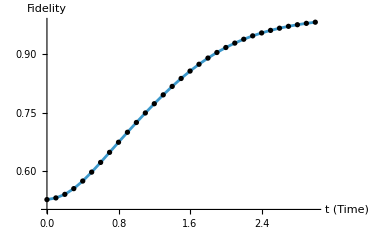

```mathematica
ListLinePlot[similarities,]
```

We can find the steady state of the evolution when ρ̇=0, which amounts to finding the null space of ℒ or solving ℒ(ρ)=0:

```mathematica
ρsteady = Partition[NullSpace[ℒ["Matrix"]][[1]],$FockSize];
```

Fidelity distance between the steady state and |-2ⅈ G/γ⟩:

```mathematica
QuantumDistance[QuantumState[ ρsteady,$FockSize]["Normalize"],CoherentState[][-I 2G/γ]]
```

2.60287×10^-8

If we have an initial vacuum state  ρ̂(0) = |0⟩ ⟨0| at short enough times we ignore dissipation. The evolution will be unitary and we will get a coherent state  of the form | -ⅈ G t ⟩⟨- ⅈ G t | independent of γ . Fidelity remains around 1 for small times until the approximation is no longer valid

Evolving the ground state:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,FockState[0],{t,0,3}];
```

Auxiliary variables for time steps and Fock numbers:

```mathematica
time = Range[0,0.8,0.02];
fock =Range[$FockSize]-1;
```

Computing fidelity and mean photon number:

```mathematica
qs = QuantumSimilarity[CoherentState[][-I G #],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plot the statistics:

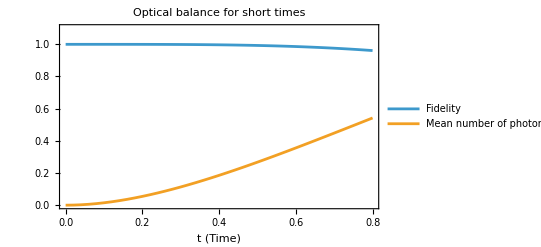

```mathematica
ListLinePlot[Thread[{time,#}]&/@{qs,meanN},]
```

### Thermalization master equation

A thermalization master equation in quantum optics describes how a system (e.g., a qubit or harmonic oscillator) drives towards a thermal Gibbs state ρ_th=ⅇ^(-β H)/Z via interaction with a reservoir. Under Born-Markov and rotating-wave approximations, this typically yields a Lindblad master equation with damping and excitation rates satisfying local detailed balance

Master equation:

dρ/dt=-ⅈ[H,ρ]+κ(n_th+1)𝒟[â]ρ+κ n_th 𝒟[(â)^†]ρ

where n_th is the thermal photon number that is dependent on temperature and frequency of the cavity, and κ is the decay photon rate. We now include both a and a^† as Lindblad jump operators(photon loss and photon injection channels)

Set up truncation size:

```mathematica
SetFockSpaceSize[25];
```

Final evolution time:

```mathematica
tf = 10.;
```

Setting the master equation (Ĥ=ℏ ω a^†a) with the relevant jump operators:

```mathematica
ℒ = QuantumOperator["Liouvillian"[ ω SuperDagger[a]@a,{a,SuperDagger[a]},{κ(nth+1),κ nth}],"Parameters"->{ω,κ,nth}];
```

Pick some parameters, for example n_th = 3, ω = 1, κ = 0.6 :

```mathematica
liouville =ℒ[1,0.6,3];
```

Calculating mean number of photons for different initial Fock states:

```mathematica
meanPhotons =
Table[ρt = QuantumEvolve[ⅈ liouville ,FockState[i],{t,0,tf}];Table[{t,Dot[Range[0,$FockSize-1],Diagonal[ρt[t]["DensityMatrix"]]]},{t,0,tf,0.01}],{i,{0,1,4}}];
```

Plot mean number of photons, see the convergence towards n_th:

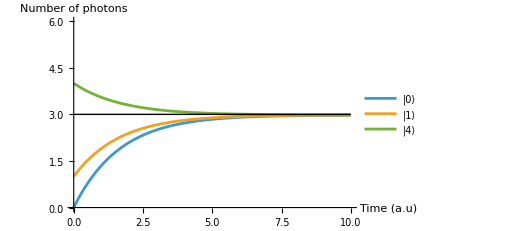

```mathematica
ListLinePlot[meanPhotons,]
```

It indeed converges to a thermal state with n_th mean number of photons:

```mathematica
QuantumSimilarity[ρt[tf],ThermalState[3.]]
```

0.999624

Find the steady state:

```mathematica
ρsteady =Chop[Partition[NullSpace[liouville["Matrix"]][[1]],$FockSize]];
```

Verify it is the thermal state with n_th=3:

```mathematica
Chop[QuantumState[ρsteady,$FockSize]["Normalize"]-ThermalState[3.]]
```

0

Changing the κ parameter, compute evolved states:

```mathematica
evolved =Table[QuantumEvolve[ⅈ ℒ[1,k,3],FockState[0],{t,0,tf}],{k,{0.5,1.,1.5}}];
```

Calculate again the mean number of photons:

```mathematica
meanPhotons =Table[{t,Dot[Range[0,$FockSize-1],Diagonal[#[t]["DensityMatrix"]]]},{t,0,tf,0.01}]&/@evolved;
```

Plot the curves, we see change in the rate of convergence such that higher κ converges faster:

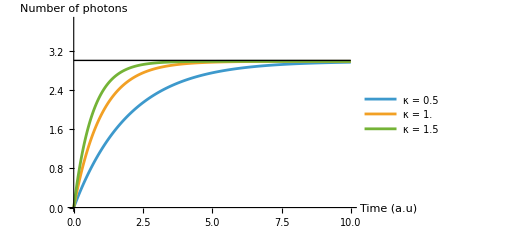

```mathematica
ListLinePlot[meanPhotons,]
```

### Jaynes-Cummings with dissipation

We revisit the Jaynes-Cummings model but now including jump operators related to energy dissipation. So we have the following master equation

Ĥ=ℏ ν (â)^†â+1/2 ℏ ω σ_z+ℏ g (σ_- (â)^†+σ_+ â)

(d ρ)/(d t)=-ⅈ/ℏ[Ĥ,ρ]+𝒟[σ_-]ρ+𝒟[â]ρ

So the jump operators are  L_decay=√γ_1(σ_- ⊗ ℐ) and L_loss = √γ_2(ℐ ⊗ a) associated to dissipation rates γ_1 and γ_2 of the atom decaying or the field losing photons

Annihilation operator in the second qudit:

```mathematica
a:= AnnihilationOperator[{2}];
```

Atomic operators:

```mathematica
atomBasis = QuantumBasis[{"e","g"}];
σplus = QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];
```

Setting up parameters for field frequency, atomic frequency and interaction coupling, we consider a resonant case (ν = ω)

```mathematica
SetFockSpaceSize[8];
ν = 10.;   (* field frequency *)
ω = 10.;   (* atomic frequency *)
gc = 15.; (* interaction coupling strength *)
```

Let’s consider an initial state |e⟩ |n⟩ with n = 2:

```mathematica
ψ0 = QuantumTensorProduct[QuantumState["0",atomBasis],FockState[2]]
```

e2

Jaynes-Cummings Hamiltonian:

```mathematica
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Jump operators:

```mathematica
decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;
```

Get the probability of finding the atom in the excited state:

```mathematica
atomProb[evolved_,tspecs_] := Table[{t, (SuperDagger[QuantumState["0",atomBasis]]@evolved[t])["Norm"]}, Evaluate[{t, Sequence@@tspecs}]]
```

Let’s calculate the evolution for different damping parameters such that γ_1=γ_2, saving the probability of finding the atom in the excited state. QuantumOperator  also admits the “Hamiltonian” syntax to include jump operators, ⅈ is not needed when using QuantumEvolve in this case.

```mathematica
probsE = Table[ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {x, x}]];
   evolved = QuantumEvolve[ ℋ, ψ0, {t, 0, 2}];
   atomProb[evolved,{0,2,0.01}],
   {x, {0.8, 0.4, 0.2}}];
```

Damped Rabi oscillations:

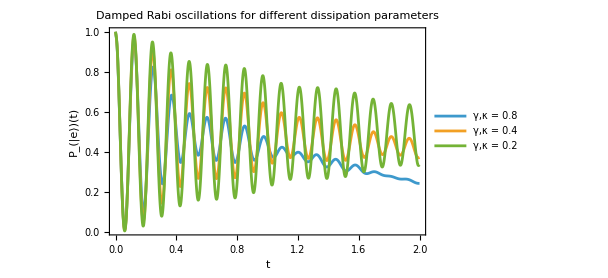

```mathematica
ListLinePlot[probsE,]
```

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
```

Exercises

What jump operator do you think represents dephasing for a bosonic mode? Generate an animation of the evolution of the density matrix of a uniform superposition state, under the dephasing channel (with  H=0)

Solution

Generate a uniform superposition state:

ρ = QuantumState["UniformSuperposition",$FockSize];

Dephasing can be modelled with the jump operator a^†a:

ℒ = QuantumOperator["Liouvillian"[ None,{a["Dagger"]@a},{κϕ}],"Parameters"->{κϕ}];

Evolution of the state:

evolved =QuantumEvolve[ⅈ ℒ[0.2], ρ,{t,0,10}];

Get frames:

frames = Table[MatrixPlot[evolved[t]["DensityMatrix"],ColorFunction->"RedBlueTones",PlotLegends->All, PlotLabel->StringForm["t = ``",Round[t,0.01]],ImageSize->300,ImageMargins->20,LabelStyle->13],{t,10^-6,5,0.1}];

Export the GIF:

Export[NotebookDirectory[]<>"Dephasing.GIF",frames,"GIF","DisplayDurations"->Reverse@Subdivide[0.1,0.5,Length[frames]-1]];

Energy exchange between cavities (allowing decay) can be modelled with the jump operator (μ a_1 - λ a_2^†), where μ and λ are parameters. Consider an initial state |1,1⟩ and μ>λ. How does the entanglement of the two mode system behaves as function of time?

Solution

Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]

Set the size of the Fock space:

SetFockSpaceSize[10];

Operators of the two modes:

{a,b}=Array[AnnihilationOperator[{#}]&,2];

Initial state:

ρ0 = FockState[{1,1}];

Setting μ and λ:

{μ,λ}={0.6,0.2};

Build Liouvillian with jump operator μ a - λ b^†:

ℒ =QuantumOperator["Liouvillian"[None,{μ a - λ b^†},{0.6}]];

Evolve the state:

evolved=QuantumEvolve[I ℒ,ρ0,{t,0,4}];

Plot the measure of entanglement:

ListLinePlot[Table[QuantumEntanglementMonotone[evolved[t],{{1},{2}},"LogNegativity"],{t,0,4,0.1}],DataRange->{0,4},AxesLabel->{"t","LogNegativity"},PlotRange->All]

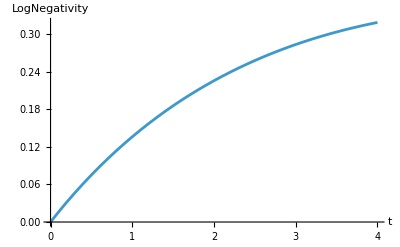

In the last section we saw the dissipative Jaynes-Cummings with a Fock state, now observe how collapse and revivals change with dissipation. The point of this exercise is to encourage exploration and determine relevant parameters. There are different regimes of interaction, so changing the Hamiltonian parameters and the γ rates can result in diverse dynamics.

Solution

Set the truncation size and relevant parameters:

SetFockSpaceSize[20];
ν = 8.;   
ω = 8.;   
gc = 10.; 
γ1 = 0.5;
γ2 = 0.5;
a:= AnnihilationOperator[{2}];

Hamiltonian:

H =  ν a^†@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@a^†);

Master equation set up:

decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;

ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {γ1, γ2}]];

Initial state:

ρ0 =QuantumTensorProduct[QuantumState["1",atomBasis],CoherentState[][3.]];

Evolution:

evolved = QuantumEvolve[ℋ, ρ0,{t,0,10}];

Plotting results:

probs = atomProb[evolved,{0,10,0.1}];
ListLinePlot[probs,InterpolationOrder->2,PlotRange->All,PlotStyle->Red]

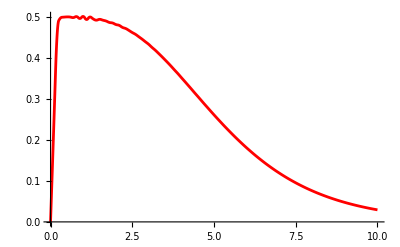

Comparing with the case without dissipation, already with γ_1=γ_2=0.5 all oscillations disappear:

Show[%326,%356]

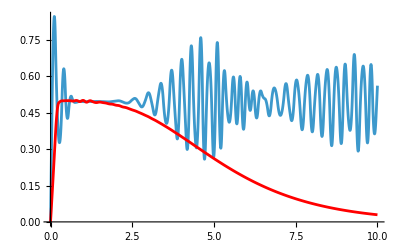

References

Gerry, Christopher C., and Peter L. Knight. Introductory Quantum Optics. Cambridge: Cambridge University Press, 2005.

Breuer, Heinz-Peter, and Francesco Petruccione. The Theory of Open Quantum Systems. Oxford: Oxford University Press, 2002.

Banerjee, Subhashish. Open Quantum Systems: Dynamics of Nonclassical Evolution. Singapore: Springer, 2018

Barnett, Stephen M., and Paul M. Radmore. Methods in Theoretical Quantum Optics. Oxford: Oxford University Press, 1997.

Carmichael, Howard J. Statistical Methods in Quantum Optics 1: Master Equations and Fokker-Planck Equations. Berlin: Springer, 1999

Scully, Marlan O., and M. Suhail Zubairy. Quantum Optics. Cambridge: Cambridge University Press, 1997.

Walls, D. F., and Gerard J. Milburn. Quantum Optics. 2nd ed. Berlin: Springer, 2008.